## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=0.2; Q=0.99;
```

```mathematica
winit=(0.15-0.00005*I)
```

0.15-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.1779-1.52193×10^-9 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.173522

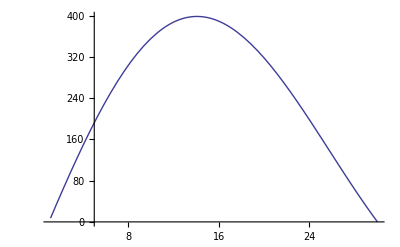

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,200}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,200}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,-1.51366×10^-9},{30.2,-1.21704×10^-9},{30.4,-9.44042×10^-10},{30.6,-6.86327×10^-10},{30.8,-4.56452×10^-10},{31.,-2.39295×10^-10},{31.2,-6.77954×10^-12},{31.4,1.4695×10^-10},{31.6,3.17907×10^-10},{31.8,4.75011×10^-10},{32.,6.14847×10^-10},{32.2,7.52627×10^-10},{32.4,8.76316×10^-10},{32.6,9.88944×10^-10},{32.8,1.09279×10^-9},{33.,1.19974×10^-9},{33.2,1.27488×10^-9},{33.4,1.35469×10^-9},{33.6,1.42648×10^-9},{33.8,1.49266×10^-9},{34.,1.55257×10^-9},{34.2,1.60716×10^-9},{34.4,1.65647×10^-9},{34.6,1.70113×10^-9},{34.8,1.74103×10^-9},{35.,1.77637×10^-9},{35.2,1.8132×10^-9},{35.4,1.83638×10^-9},{35.6,1.86099×10^-9},{35.8,1.88241×10^-9},{36.,1.90057×10^-9},{36.2,1.9219×10^-9},{36.4,1.92955×10^-9},{36.6,1.94216×10^-9},{36.8,1.94919×10^-9},{37.,1.95524×10^-9},{37.2,1.95979×10^-9},{37.4,1.96316×10^-9},{37.6,1.96307×10^-9},{37.8,1.96241×10^-9},{38.,1.96042×10^-9},{38.2,1.95701×10^-9},{38.4,1.95202×10^-9},{38.6,1.9466×10^-9},{38.8,1.93977×10^-9},{39.,1.93196×10^-9},{39.2,1.92115×10^-9},{39.4,1.91366×10^-9},{39.6,1.90332×10^-9},{39.8,1.89225×10^-9},{40.,1.88205×10^-9},{40.2,1.86829×10^-9},{40.4,1.85546×10^-9},{40.6,1.84212×10^-9},{40.8,1.82683×10^-9},{41.,1.84091×10^-9},{41.2,1.79954×10^-9},{41.4,1.78462×10^-9},{41.6,1.7694×10^-9},{41.8,1.75616×10^-9},{42.,1.74836×10^-9},{42.2,1.7221×10^-9},{42.4,1.70559×10^-9},{42.6,1.6899×10^-9},{42.8,1.6734×10^-9},{43.,1.65694×10^-9},{43.2,1.64517×10^-9},{43.4,1.62359×10^-9},{43.6,1.60608×10^-9},{43.8,1.59002×10^-9},{44.,1.57316×10^-9},{44.2,1.55634×10^-9},{44.4,1.53949×10^-9},{44.6,1.52268×10^-9},{44.8,1.50587×10^-9},{45.,1.48911×10^-9},{45.2,1.47241×10^-9},{45.4,1.45574×10^-9},{45.6,1.43914×10^-9},{45.8,1.42277×10^-9},{46.,1.40615×10^-9},{46.2,1.38981×10^-9},{46.4,1.37354×10^-9},{46.6,1.35739×10^-9},{46.8,1.34483×10^-9},{47.,1.32541×10^-9},{47.2,1.30954×10^-9},{47.4,1.29383×10^-9},{47.6,1.2784×10^-9},{47.8,1.26278×10^-9},{48.,1.24744×10^-9},{48.2,1.23224×10^-9},{48.4,1.21698×10^-9},{48.6,1.20009×10^-9},{48.8,1.1874×10^-9},{49.,1.17276×10^-9},{49.2,1.15823×10^-9},{49.4,1.14385×10^-9},{49.6,1.12963×10^-9},{49.8,1.11557×10^-9},{50.,1.1016×10^-9},{50.2,1.08798×10^-9},{50.4,1.0681×10^-9},{50.6,1.0608×10^-9},{50.8,1.04734×10^-9},{51.,1.03413×10^-9},{51.2,1.02107×10^-9},{51.4,1.00816×10^-9},{51.6,9.95409×10^-10},{51.8,9.82802×10^-10},{52.,9.70377×10^-10},{52.2,9.58149×10^-10},{52.4,9.4583×10^-10},{52.6,9.3383×10^-10},{52.8,9.21943×10^-10},{53.,9.10189×10^-10},{53.2,8.98662×10^-10},{53.4,8.87131×10^-10},{53.6,8.75899×10^-10},{53.8,8.64667×10^-10},{54.,8.53616×10^-10},{54.2,8.42739×10^-10},{54.4,8.31998×10^-10},{54.6,8.21696×10^-10},{54.8,8.1084×10^-10},{55.,8.00462×10^-10},{55.2,7.90018×10^-10},{55.4,7.80331×10^-10},{55.6,7.70282×10^-10},{55.8,7.60378×10^-10},{56.,7.50655×10^-10},{56.2,7.41143×10^-10},{56.4,7.31634×10^-10},{56.6,7.26586×10^-10},{56.8,7.13141×10^-10},{57.,7.04051×10^-10},{57.2,6.94831×10^-10},{57.4,6.86139×10^-10},{57.6,6.77486×10^-10},{57.8,6.68863×10^-10},{58.,6.60285×10^-10},{58.2,6.51889×10^-10},{58.4,6.33604×10^-10},{58.6,6.35443×10^-10},{58.8,6.27434×10^-10},{59.,6.19412×10^-10},{59.2,6.11561×10^-10},{59.4,6.03879×10^-10},{59.6,5.96182×10^-10},{59.8,5.88577×10^-10},{60.,5.81215×10^-10},{60.2,5.73907×10^-10},{60.4,5.66607×10^-10},{60.6,5.59373×10^-10},{60.8,5.5241×10^-10},{61.,5.45435×10^-10},{61.2,5.38618×10^-10},{61.4,5.319×10^-10},{61.6,5.25223×10^-10},{61.8,5.18642×10^-10},{62.,5.12106×10^-10},{62.2,5.0584×10^-10},{62.4,4.99413×10^-10},{62.6,4.93132×10^-10},{62.8,4.8703×10^-10},{63.,4.80874×10^-10},{63.2,4.73945×10^-10},{63.4,4.69018×10^-10},{63.6,4.63191×10^-10},{63.8,4.5749×10^-10},{64.,4.5182×10^-10},{64.2,4.45334×10^-10},{64.4,4.40672×10^-10},{64.6,4.35263×10^-10},{64.8,4.31335×10^-10},{65.,4.24548×10^-10},{65.2,4.19367×10^-10},{65.4,4.1421×10^-10},{65.6,4.09081×10^-10},{65.8,4.04077×10^-10},{66.,4.02131×10^-10},{66.2,3.94864×10^-10},{66.4,3.89409×10^-10},{66.6,3.86436×10^-10},{66.8,3.80042×10^-10},{67.,3.7534×10^-10},{67.2,3.51844×10^-10},{67.4,3.6639×10^-10},{67.6,3.61833×10^-10},{67.8,3.57446×10^-10},{68.,3.53206×10^-10},{68.2,3.48891×10^-10},{68.4,3.4468×10^-10},{68.6,3.40196×10^-10},{68.8,3.35185×10^-10},{69.,3.32811×10^-10},{69.2,3.2837×10^-10},{69.4,3.24434×10^-10},{69.6,3.20658×10^-10},{69.8,3.16717×10^-10},{70.,3.1296×10^-10}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<51,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,50}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,50}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,-1.51366×10^-9},{29.8,-1.82417×10^-9},{29.6,-2.18101×10^-9},{29.4,-2.55268×10^-9},{29.2,-2.9612×10^-9},{29.,-3.40363×10^-9},{28.8,-3.87222×10^-9},{28.6,-4.38336×10^-9},{28.4,-4.93852×10^-9},{28.2,-5.5358×10^-9},{28.,-6.1832×10^-9},{27.8,-6.8833×10^-9},{27.6,-7.64001×10^-9},{27.4,-8.46011×10^-9},{27.2,-9.34835×10^-9},{27.,-1.03098×10^-8},{26.8,-1.1352×10^-8},{26.6,-1.24805×10^-8},{26.4,-1.37058×10^-8},{26.2,-1.50345×10^-8},{26.,-1.64767×10^-8},{25.8,-1.80426×10^-8},{25.6,-1.97444×10^-8},{25.4,-2.15941×10^-8},{25.2,-2.3607×10^-8},{25.,-2.57968×10^-8},{24.8,-2.81844×10^-8},{24.6,-3.07851×10^-8},{24.4,-3.36218×10^-8},{24.2,-3.67168×10^-8},{24.,-4.01142×10^-8},{23.8,-4.3799×10^-8},{23.6,-4.78425×10^-8},{23.4,-5.22701×10^-8},{23.2,-5.71201×10^-8},{23.,-6.24399×10^-8},{22.8,-6.82791×10^-8},{22.6,-7.46875×10^-8},{22.4,-8.175×10^-8},{22.2,-8.95167×10^-8},{22.,-9.80324×10^-8},{21.8,-1.07516×10^-7},{21.6,-1.17937×10^-7},{21.4,-1.29458×10^-7},{21.2,-1.42219×10^-7},{21.,-1.5624×10^-7},{20.8,-1.71996×10^-7},{20.6,-1.89385×10^-7},{20.4,-2.08722×10^-7},{20.2,-2.30262×10^-7},{20.,-2.54231×10^-7}}

```mathematica
(*The imaginary part vs the radius*)
```

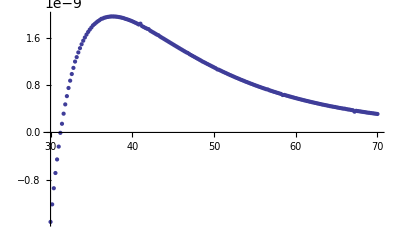

```mathematica
ListPlot[{t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

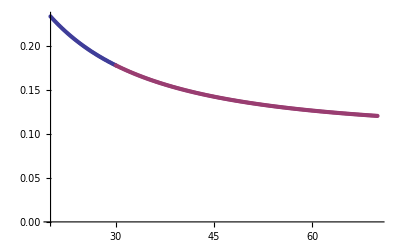

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=0.2/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=0.2/I.dat",Join[t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=0.2/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=0.2/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```